{{0.4,0},{12.5,0.0128},{25.,0.0331},{37.5,0.0664},{50.,0.236},{52.5,0.69},{53.8,1.1},{55.,1.9},{62.5,8.6},{75.,20.6},{87.5,33.1},{99.7,45.}}

FittedModel[Piecewise[{{-0.110125+0.00955059 x, x<53.5431}, {-51.0673+0.961255 x, x≥53.5431}, {0, True}}]]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.00955059 | 0.00670944 | 1.42346 | 0.192412
b | 0.961255 | 0.00752023 | 127.823 | 1.56889×10^-14
c | -0.110125 | 0.236326 | -0.465988 | 0.653649
k | 53.5431 | 0.293532 | 182.41 | 9.12978×10^-16

{Piecewise[{{-51.0673+0.961255 x-2.306 √(0.311489-0.00817203 x+0.0000565538 x^2), x≥53.5431}, {-0.110125+0.00955059 x-2.306 √(0.05585-0.00266949 x+0.0000450166 x^2), True}}],Piecewise[{{-51.0673+0.961255 x+2.306 √(0.311489-0.00817203 x+0.0000565538 x^2), x≥53.5431}, {-0.110125+0.00955059 x+2.306 √(0.05585-0.00266949 x+0.0000450166 x^2), True}}]}

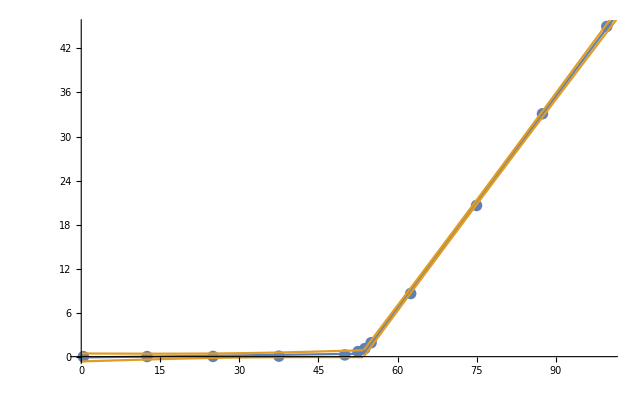

```mathematica
data = Import["~/mnt/phys3117/lab1/3.3-data", "tsv"][[2;;All,{1,2}]]
fit = NonlinearModelFit[data, Piecewise[{{a x + c, x < k}, {b x + (a k + c - b k), x ≥ k}}], {a, b, c, {k, 53}}, x]
fit["ParameterTable"]
fit["MeanPredictionBands"]
Show[ListPlot[data], Plot[{Normal[fit], fit["MeanPredictionBands"]}, {x, 0, 200}]]
```

```mathematica
Sqrt@Length[data] 1.96fit["ParameterErrors"]
```

{0.0455363,0.051039,1.60392,1.99215}

```mathematica
{0.9612545644613429,0.05103903218053276}/2.7
```

{0.35602,0.0189033}